# Spatial ARGs

```mathematica
ClearAll
```

ClearAll

#### Two Formulas for Root Locations

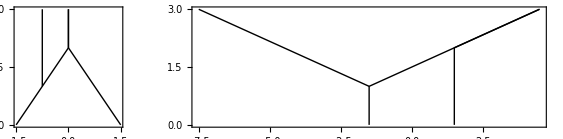
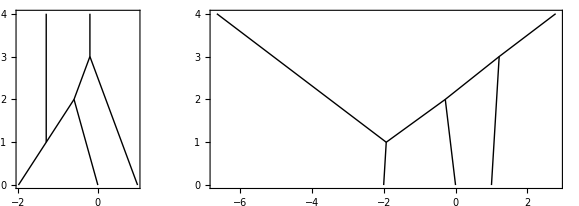
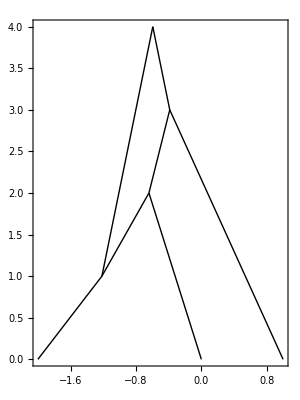
Throughout here and in the appendix of the manuscript, I use the notation .
The root locations currently in the manuscript main text (Eq 10),  is obtained by maximizing the likelihood function given by Eq 6 in which the exponent is  proportional to . However Eq 6 is not a probability density function in , i.e., it doesn’t integrate to 1. But turns out this is identical to Osmond and Coop Method (without importance sampling and epochs), where  in their case is  size block diagonal matrix, with  diagonal matrices are of size  corresponding to the shared time of each tree ( = number of trees). I will call this the Old Method. 

With correct normalizing, see Appendix of the Manuscript, we have Eq 35 as the correct likelihood function with the exponent being proportional to   where  is the expected locations of the samples given a forward in time model of Brownian motion starting at the roots, . The MLE for the root location is then given by the solution to the system of equations 
Following are the calculations to compare the two estimates for toy examples. The summary of the results are given below

ARGd | Old Method                                                     New Method                          | Single Root
 | -Graphics-  | 
-Graphics- | -Graphics- | -Graphics-
While the two methods give very different locations for the case of multiple, they reduce to the same values for the case of a single root. While the second method uses the correct conditional distribution, the estimates look weird. On the other, the old method uses the incorrect distribution.
Further, the old method necessitates that there are more samples than roots to get a meaningful solution which is not the case for the old method. It makes sense that you need more samples than roots, otherwise there are enough degrees of freedom (due to the free roots) to adjust the values of samples, leading to a zero dispersal rate.

```mathematica
RootLocationOld[P_,R_,l_,SpInv_]:=((*See Equation 10 in Manuscript*)RR=Transpose[R].SpInv.R;
RP=Transpose[R].SpInv.P;
PP=Transpose[P].SpInv.P;
Inverse[RR].RP.l//Simplify)
RootLocationNew[P_,R_,l_,SpInv_]:=((*See Equation 44 in Manuscript*)RR=Transpose[R].SpInv.R;
RP=Transpose[R].SpInv.P;
PP=Transpose[P].SpInv.P;
Inverse[RP.Inverse[PP].Transpose[RP]].RP.l//Simplify)
DispersalRate[lp_,μp_,SpInv_,n_]:=Transpose[lp-μp].SpInv.(lp-μp)/n
```

ARG 1

```mathematica
Sp = {{t,t13,0},{t13, t, t46},{0, t46, t}}/. t->t1+t2+t3/.t13->t1/.t46->t3;
Sp//MatrixForm
R = {{1,0},{0,1},{0,1}};
(*R = {{1},{1},{1}};*)
R//MatrixForm
P = { {1,0} ,{1,0} ,{0,1} } ;
P//MatrixForm
```

(t1+t2+t3 | t1 | 0
t1 | t1+t2+t3 | t3
0 | t3 | t1+t2+t3)

(1 | 0
0 | 1
0 | 1)

(1 | 0
1 | 0
0 | 1)

```mathematica
l = {{l1},{l2}}
SpInv = Inverse[Sp]//Simplify;
SpInv//MatrixForm
muOld = RootLocationOld[P,R,l,SpInv]//Simplify (* Using the Old Formula*)
muNew = RootLocationNew[P,R,l,SpInv] (* Using the New Formula*)
```

{{l1},{l2}}

(((t1+t2) (t1+t2+2 t3))/(2 t1^2 (t2+t3)+t2 (t2^2+3 t2 t3+2 t3^2)+t1 (3 t2^2+6 t2 t3+2 t3^2)) | -t1/(2 t1 (t2+t3)+t2 (t2+2 t3)) | (t1 t3)/(2 t1^2 (t2+t3)+t2 (t2^2+3 t2 t3+2 t3^2)+t1 (3 t2^2+6 t2 t3+2 t3^2))
-t1/(2 t1 (t2+t3)+t2 (t2+2 t3)) | (t1+t2+t3)/(2 t1 (t2+t3)+t2 (t2+2 t3)) | -t3/(2 t1 (t2+t3)+t2 (t2+2 t3))
(t1 t3)/(2 t1^2 (t2+t3)+t2 (t2^2+3 t2 t3+2 t3^2)+t1 (3 t2^2+6 t2 t3+2 t3^2)) | -t3/(2 t1 (t2+t3)+t2 (t2+2 t3)) | ((t2+t3) (2 t1+t2+t3))/(2 t1^2 (t2+t3)+t2 (t2^2+3 t2 t3+2 t3^2)+t1 (3 t2^2+6 t2 t3+2 t3^2)))

{{(l2 t1+l1 (t1+2 t2))/(2 (t1+t2))},{(l1+l2)/2}}

{{(-l2 (t2+t3)+l1 (2 t2+t3))/t2},{(-l1 t3+l2 (t2+t3))/t2}}

```mathematica
sigmaOld = Transpose[P.l - R.muOld].SpInv.(P.l - R.muOld)/n //Simplify
sigmaNew = Transpose[P.(l-Inverse[Transpose[P].SpInv.P].Transpose[P].SpInv.R.muNew)].SpInv.P.(l-Inverse[Transpose[P].SpInv.P].Transpose[P].SpInv.R.muNew)//Simplify
```

{{(l1-l2)^2/(2 n (t1+t2))}}

{{0}}

Location of 3

```mathematica
sa = {{t2+t3},{0},{0}};
mu3Old = muOld[[1,1]]+Transpose[sa].SpInv.(P.l-R.muOld)//Simplify
mu3New = muNew[[1,1]]+Transpose[sa].SpInv.(P.l-R.muNew )//Simplify
(*mu3New = muNew[[1,1]]+Transpose[sa].SpInv.P.(l-Inverse[Transpose[P].SpInv.P].Transpose[P].SpInv.R.muNew )//Simplify*)
```

{{(l2 t1+l1 (t1+2 t2))/(2 (t1+t2))}}

{{l1}}

Location of 4

```mathematica
sb = {{0},{t3},{t3}} 
mu4Old = muOld[[2,1]]+Transpose[sb].SpInv.(P.l-R.muOld)//Simplify
(*mu4New = muNew[[2,1]]+Transpose[sb].SpInv.P.(l-Inverse[Transpose[P].SpInv.P].Transpose[P].SpInv.R.muNew )//Simplify*)
mu4New = muNew[[2,1]]+Transpose[sb].SpInv.(P.l-R.muNew )//Simplify
```

{{0},{t3},{t3}}

{{(l1+l2)/2}}

{{l2}}

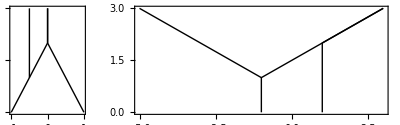

```mathematica
ParamValues = {l1->-1,l2->1,t1->1,t2->1,t3->1};Line1 = Graphics[Line[{{l1,0},{mu3Old[[1,1]],t1},{mu4Old[[1,1]],t1+t2},{muOld[[2,1]],t1+t2+t3}}]]/.ParamValues;
Line2 = Graphics[Line[{{mu3Old[[1,1]],t1},{muOld[[1,1]],t1+t2+t3}}]]/.ParamValues;
Line3= Graphics[Line[{{l2,0},{mu4Old[[1,1]],t1+t2},{muOld[[2,1]],t1+t2+t3}}]]/.ParamValues;
A = Show[Line1,Line2,Line3, Frame->True];

Line1 = Graphics[Line[{{l1,0},{mu3New[[1,1]],t1},{mu4New[[1,1]],t1+t2},{muNew[[2,1]],t1+t2+t3}}]]/.ParamValues;
Line2 = Graphics[Line[{{mu3New[[1,1]],t1},{muNew[[1,1]],t1+t2+t3}}]]/.ParamValues;
Line3= Graphics[Line[{{l2,0},{mu4New[[1,1]],t1+t2},{muNew[[2,1]],t1+t2+t3}}]]/.ParamValues;
B= Show[Line1,Line2,Line3, Frame->True];

GraphicsRow[{A,B}]
```

Likelihood Function

```mathematica
RP=Transpose[R].SpInv.P;
PP=Transpose[P].SpInv.P;
Det[Inverse[PP]]/.ParamValues
sigmaNew
L[μ1_,μ2_,σ_]:= (l = {{l1},{l2}};
μ={{μ1},{μ2}};
μl = Inverse[PP].Transpose[RP].μ; 
Exp[-1/(2 σ^2) Transpose[l - μl].PP.(l-μl)/( Sqrt[(2 Pi σ^2)^2 Det[Inverse[PP]]] ) ]//Simplify)
μ1
L[μ1,μ2,sigmaNew]//Simplify

(*L[m1_,m2_,σ_]:= (  l = {{l1},{l2}};
μ={{μ1},{μ2}};
μl = Inverse[PP].Transpose[PR].μ; 
Exp[-1/(2 σ^2) Transpose[l - μl].SpInv.(l-μl)/( Sqrt[(2 Pi σ^2)^2 Det[Inverse[PP]]] ) ]//Simplify
)
*)(*L[μ1,μ2,sigmaNew]*)
```

21/4

{{0}}

μ1

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

{{Indeterminate}}

ARG 2 
-Graphics-

```mathematica
Sp = {{t,t14,0,0},{t14, t,t58, t68},{0, t58, t, t68},{0,t68,t68,t}}/. t->t1+t2+t3+t4/.t14->t1/.t58->t3+t4/.t68->t4;
Sp//MatrixForm
R = {{1,0},{0,1},{0,1},{0,1}};
(*R = {{1},{1},{1},{1}};*)
R//MatrixForm
P = { {1,0,0} ,{1,0,0} ,{0,1,0},{0,0,1}} ;
P//MatrixForm
```

(t1+t2+t3+t4 | t1 | 0 | 0
t1 | t1+t2+t3+t4 | t3+t4 | t4
0 | t3+t4 | t1+t2+t3+t4 | t4
0 | t4 | t4 | t1+t2+t3+t4)

(1 | 0
0 | 1
0 | 1
0 | 1)

(1 | 0 | 0
1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
l = {{l1},{l2},{l3}};
SpInv = Inverse[Sp]//Simplify;
SpInv//MatrixForm;
muOld = RootLocationOld[P,R,l,SpInv]//Simplify; (* Using the Old Formula*)
muNew = RootLocationNew[P,R,l,SpInv]//Simplify ; (* Using the New Formula*)

s4 = {{t2+t3+t4},{0},{0},{0}};
s5 = {{0},{t3+t4},{t3+t4},{t4}};
s6 = {{0},{t4},{t4},{t4}};
mu4Old = muOld[[1,1]]+Transpose[s4].SpInv.(P.l-R.muOld)//Simplify;
mu4New = muNew[[1,1]]+Transpose[s4].SpInv.(P.l-R.muNew )//Simplify;
mu5Old = muOld[[2,1]]+Transpose[s5].SpInv.(P.l-R.muOld)//Simplify;
mu5New = muNew[[2,1]]+Transpose[s5].SpInv.(P.l-R.muNew )//Simplify;
mu6Old = muOld[[2,1]]+Transpose[s6].SpInv.(P.l-R.muOld)//Simplify;
mu6New = muNew[[2,1]]+Transpose[s6].SpInv.(P.l-R.muNew )//Simplify;


sigmaOld = Transpose[P.l - R.muOld].SpInv.(P.l - R.muOld)/n //Simplify;
sigmaNew = Transpose[P.(l-Inverse[Transpose[P].SpInv.P].Transpose[P].SpInv.R.muNew)].SpInv.P.(l-Inverse[Transpose[P].SpInv.P].Transpose[P].SpInv.R.muNew)/n//Simplify;
```

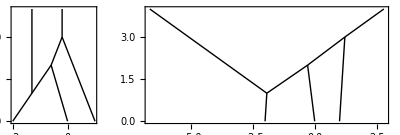

```mathematica
ParamValues = {l1->-2,l2->0, l3->1,t1->1,t2->1,t3->1,t4->1,n->3};
Line1 = Graphics[Line[{{l1,0},{mu4Old[[1,1]],t1},{mu5Old[[1,1]],t1+t2},{mu6Old[[1,1]],t1+t2+t3},{muOld[[2,1]],t1+t2+t3+t4}}]]/.ParamValues;
Line2 = Graphics[Line[{{mu4Old[[1,1]],t1},{muOld[[1,1]],t1+t2+t3+t4}}]]/.ParamValues;
Line3= Graphics[Line[{{l2,0},{mu5Old[[1,1]],t1+t2}}]]/.ParamValues;
Line4= Graphics[Line[{{l3,0},{mu6Old[[1,1]],t1+t2+t3}}]]/.ParamValues;
A = Show[Line1,Line2,Line3,Line4, Frame->True];

Line1 = Graphics[Line[{{l1,0},{mu4New[[1,1]],t1},{mu5New[[1,1]],t1+t2},{mu6New[[1,1]],t1+t2+t3},{muNew[[2,1]],t1+t2+t3+t4}}]]/.ParamValues;
Line2 = Graphics[Line[{{mu4New[[1,1]],t1},{muNew[[1,1]],t1+t2+t3+t4}}]]/.ParamValues;
Line3= Graphics[Line[{{l2,0},{mu5New[[1,1]],t1+t2}}]]/.ParamValues;
Line4= Graphics[Line[{{l3,0},{mu6New[[1,1]],t1+t2+t3}}]]/.ParamValues;
B= Show[Line1,Line2,Line3,Line4, Frame->True];
GraphicsRow[{A,B}]
```

```mathematica
RP=Transpose[R].SpInv.P/.ParamValues;
PP=Transpose[P].SpInv.P/.ParamValues;
Det[Inverse[PP]]/.ParamValues
sigmaNew/.ParamValues
L[μ1_,μ2_,σ_]:= (l = {{l1},{l2},{l3}}/.ParamValues;
μ={{μ1},{μ2}};
μl = Inverse[PP].Transpose[RP].μ/.ParamValues; 
Exp[-1/(2 σ^2) Transpose[l - μl].PP.(l-μl)]/( Sqrt[(2 Pi σ^2)^3 Det[Inverse[PP]]] ) //Simplify)

Plot3D[Log[L[μ1,μ2,sigmaNew/.ParamValues]] , {μ1,-7,3},{μ2,-7,4}, AxesLabel->Automatic]
Plot3D[Log[L[μ1,μ2,sigmaNew/.ParamValues]] , {μ1,-7,-5},{μ2,2,4}, AxesLabel->Automatic]
```

161/6

{{1/42}}

-Graphics3D-

-Graphics3D-

```mathematica
Reduce[(sigmaOld/sigmaNew)[[1,1]]>=1&& t1>0&&t2>0&&t3>0&&t4>0&&l1∈Reals&&l2∈Reals&&l3∈Reals]
sigmaNew /.l1->(l2 t2-l3 t2+l2 t3)/t3//Simplify
```

(l2|l3)∈ℝ&&t3>0&&t2>0&&t4>0&&((l1<(l2 t2-l3 t2+l2 t3)/t3&&t1>0)||(l1>(l2 t2-l3 t2+l2 t3)/t3&&t1>0))

{{0}}

```mathematica
Solve[(sigmaOld/sigmaNew)[[1,1]]<1]
```

Power::infy: Infinite expression 1/0 encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Solve::naqs: ComplexInfinity<1 is not a quantified system of equations and inequalities.

Solve[ComplexInfinity<1]

```mathematica
Inverse[Transpose[P].SpInv.P].Transpose[P].SpInv.R.muNew//Simplify;
Transpose[R].SpInv.P//Simplify//MatrixForm
NullSpace[%]//Simplify
(Inverse[Transpose[P].SpInv.P].Transpose[P].SpInv.R.muNew - l)//Simplify
Inverse[Transpose[P].SpInv.P].Transpose[P].SpInv.R.{{mu7},{mu8}}//Simplify
Solve[Inverse[Transpose[P].SpInv.P].Transpose[P].SpInv.R.{{mu7},{mu8}} == l,{mu7,mu8}]
```

((t1^2 (t2+t3+t4)+t1 (2 t2^2+4 t2 (t3+t4)+t3 (t3+2 t4))+t2 (t2^2+3 t2 (t3+t4)+2 t3 (t3+2 t4)))/(-t1^2 (t1+t2+t3) (t1+t2+t3+2 t4)+(t1+t2) (t1+t2+t3+t4) (t1^2+2 t1 t2+t2^2+3 t1 (t3+t4)+3 t2 (t3+t4)+2 t3 (t3+2 t4))) | (t1 (t1 (t3+t4)+t2 (t3+t4)+t3 (t3+2 t4)))/(-t1^2 (t1+t2+t3) (t1+t2+t3+2 t4)+(t1+t2) (t1+t2+t3+t4) (t1^2+2 t1 t2+t2^2+3 t1 (t3+t4)+3 t2 (t3+t4)+2 t3 (t3+2 t4))) | (t1 (t1+t2) t4)/(-t1^2 (t1+t2+t3) (t1+t2+t3+2 t4)+(t1+t2) (t1+t2+t3+t4) (t1^2+2 t1 t2+t2^2+3 t1 (t3+t4)+3 t2 (t3+t4)+2 t3 (t3+2 t4)))
((t1+t2) (t1+t2+t3) (t2+t3+t4))/(2 t1^3 (t2+t3+t4)+t1^2 (5 t2^2+4 t3^2+8 t3 t4+3 t4^2+10 t2 (t3+t4))+2 t1 (2 t2^3+6 t2^2 (t3+t4)+t3 (t3^2+3 t3 t4+2 t4^2)+t2 (5 t3^2+10 t3 t4+3 t4^2))+t2 (t2^3+4 t2^2 (t3+t4)+2 t3 (t3^2+3 t3 t4+2 t4^2)+t2 (5 t3^2+10 t3 t4+3 t4^2))) | ((t1+t2+t3) (t2 (t2+t3+t4)+t1 (2 t2+t3+t4)))/(2 t1^3 (t2+t3+t4)+t1^2 (5 t2^2+4 t3^2+8 t3 t4+3 t4^2+10 t2 (t3+t4))+2 t1 (2 t2^3+6 t2^2 (t3+t4)+t3 (t3^2+3 t3 t4+2 t4^2)+t2 (5 t3^2+10 t3 t4+3 t4^2))+t2 (t2^3+4 t2^2 (t3+t4)+2 t3 (t3^2+3 t3 t4+2 t4^2)+t2 (5 t3^2+10 t3 t4+3 t4^2))) | (t2 (t2+2 t3) (t2+t3+t4)+t1^2 (2 t2+2 t3+t4)+t1 (3 t2^2+2 t3 (t3+t4)+2 t2 (3 t3+t4)))/(2 t1^3 (t2+t3+t4)+t1^2 (5 t2^2+4 t3^2+8 t3 t4+3 t4^2+10 t2 (t3+t4))+2 t1 (2 t2^3+6 t2^2 (t3+t4)+t3 (t3^2+3 t3 t4+2 t4^2)+t2 (5 t3^2+10 t3 t4+3 t4^2))+t2 (t2^3+4 t2^2 (t3+t4)+2 t3 (t3^2+3 t3 t4+2 t4^2)+t2 (5 t3^2+10 t3 t4+3 t4^2))))

{{(t1 t3)/(t2 (t1+t2+t3)),-(t1 (t2+t3)+t2 (t2+2 t3))/(t2 (t1+t2+t3)),1}}

{{(t1 t3 (-l3 t2-l1 t3+l2 (t2+t3)))/(2 (t2 (t2+t3)^2+t1 (t2^2+t2 t3+t3^2)))},{((l3 t2+l1 t3-l2 (t2+t3)) (t1 (t2+t3)+t2 (t2+2 t3)))/(2 (t2 (t2+t3)^2+t1 (t2^2+t2 t3+t3^2)))},{(t2 (t1+t2+t3) (-l3 t2-l1 t3+l2 (t2+t3)))/(2 (t2 (t2+t3)^2+t1 (t2^2+t2 t3+t3^2)))}}

{{(mu7+mu8)/2},{(mu7 (t3+t4)+mu8 (2 t2+t3+t4))/(2 (t2+t3+t4))},{(mu7 t4+mu8 (2 t2+2 t3+t4))/(2 (t2+t3+t4))}}

{}

```mathematica
Solve[(mu7+mu8)/2==l1 && (mu7 (t3+t4)+mu8 (2 t2+t3+t4))/(2 (t2+t3+t4))==l2&&(mu7 t4+mu8 (2 t2+2 t3+t4))/(2 (t2+t3+t4))==l3,{mu7,mu8}]
```

{}